```mathematica
Quit[]
```

```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using QRNG (https://qrng.physik.hu-berlin.de/) as a source of randomness.

Note: You have to use QRNGSetCredentials function to provide login information required to use this backend.

QRNG tests

```mathematica
QRNGSetCredentials["jmiszczak","alama12kota"]
```

User name and password for using QRNG service set!

```mathematica
QRNGTestConnection[]
```

QRNG_SUCCESS

```mathematica
maxN=7;
qrngListTimings=Table[0,{maxN}];
```

```mathematica
qrngListTimings=Table[{ii,Mean[Table[AbsoluteTiming[TrueRandomReal[{0,1},10^ii]][[1]],{10}]]},{ii,1,maxN}]
```

{{1,0.052288},{2,0.052532},{3,0.052526},{4,0.10965},{5,0.24581},{6,1.20178},{7,10.27168}}

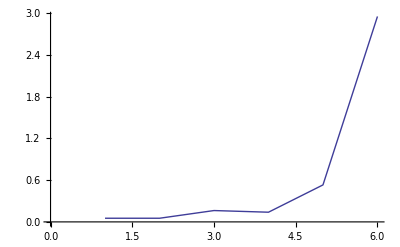

```mathematica
ListLinePlot[qrngTimings]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS/timings/v_0.2.x

```mathematica
Export["qrng_list_maxN=7_avg_of_10.dat",qrngListTimings]
```

qrng_list_maxN=7_avg_of_10.dat